## Files

11.3.0 for Mac OS X x86 (64-bit) (March 7, 2018)

1

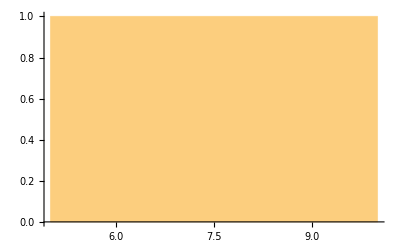

```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=2;
$Version
fns=FileNames["rays_*.bin",FileNameJoin[{NotebookDirectory[],"rays"}],∞];
fns//Length
Histogram[FileByteCount/@fns]
```

```mathematica
ClearAll[ncamString,ReadCenterFile,GetPositions,PredictAhead,DoTracking,TryConnectingTracks2,PreLabelList,ExportLabeledTracks]
ncamString[n_Integer]:=ncamString[n]=Join[{"Real32","Real32","Real32","Real32"},Join@@ConstantArray[{"UnsignedInteger8","UnsignedInteger16"},n]]
ReadCenterFile[fn_String]:=Module[{str,n,t,data,cams,other,alldata},
Print["Reading frames…"];
str=StringToStream[Import[fn,"String"]];
n=BinaryRead[str,"UnsignedInteger32"];
Print["Interpreting data…"];
t=0;
alldata=Reap[
While[n=!=EndOfFile∧t<99999999,
t+=1;
data=Table[
cams=BinaryRead[str,"UnsignedInteger8"];
If[cams==EndOfFile,
Print[fn];
Print[n];
Break[];
];
other=ncamString[cams];
(*other=BinaryRead[str,other];*)
other=BinaryReadList[str,other,1];
Prepend[other[[1]],cams]
,
{n}
];
Sow[data];
n=BinaryRead[str,"UnsignedInteger32"] (* for next frame *)
]
][[2,1]];
Close[str];
alldata
]
GetPositions[alldata_List,n_Integer]:=Module[{},
If[n<=Length[alldata],
alldata[[n,All,2;;4]]
,
{}
]
]
PreLabelList[list_List,label_]:=Map[Prepend[label],list]
ExportLabeledTracks[fnout_String,labeledtracks_List]:=Module[{trackout,tmpout,str},
tmpout=CreateFile[];
trackout=Flatten@labeledtracks;
str=OpenWrite[tmpout,BinaryFormat->True];
BinaryWrite[str,trackout,{"UnsignedInteger32","UnsignedInteger16","UnsignedInteger16","Real32","Real32","Real32"}] (* trackid, time, original ID, x, y, z *);
Close[str];
CopyFile[tmpout,fnout];
DeleteFile[tmpout];
]
PredictForwards2[track_List,n_Integer]:=Module[{last,t,tmax,ts,id},
id=track[[1,1]];
last=If[Length[track]>10,Take[track,-10],track];
tmax=last[[-1,2]];
ts=Range[tmax+1,tmax+n];
{ConstantArray[id,Length[ts]],ts,Transpose[(Fit[last[[All,{2,#}]],{1,t},t]/.t->ts)&/@Range[4,6]]}//Transpose
]
PredictBackwards2[track_List,n_Integer]:=Module[{first,t,tmin,ts,id},
id=track[[1,1]];
first=Take[track,UpTo[10]];
tmin=first[[1,2]];
ts=tmin-n;
{id,ts,(Fit[first[[All,{2,#}]],{1,t},t]/.t->ts)&/@Range[4,6]}
]
TryConnectingTracks2[trackstorage_List,connectcutoff_]:=Module[{ts,tsassoc,its,future,heads,fut,hd,dm,poss,options,Δt,usedfuture,usedpast,validoptions,components,delindex},
ts=trackstorage;
tsassoc=SortBy[#[[2]]&]/@trackstorage;
tsassoc=Association[(#[[1,1]]->#)&/@tsassoc];(* store tracks by their ID, and each track sorted by time *)
Print["Calculating and future and paste points…"];
ts=SortBy[ts,#[[1,1]]&]; (* sort by first time *)
future=PredictForwards2[#,3]&/@ts;
future=Join@@future;
heads=ts[[All,1]];
heads={#1,#2,{#4,#5,#6}}&@@@heads;
Print["Grouping by time-stamp…"];
future=GroupBy[future,#[[2]]&->Delete[2]];
heads=GroupBy[heads,#[[2]]&->Delete[2]];
{future,heads}=KeyIntersection[{future,heads}];

Print["Finding possible candidates…"];
validoptions={};
Do[
fut=future[t];
hd=heads[t];
dm=DistanceMatrix[fut[[All,2]],hd[[All,2]]];
poss=Position[dm,_?(LessThan[connectcutoff]),{2}]; (* forward prediction is close to some starting of a trajectory *)
options={fut[[#1]],hd[[#2]],dm[[#1,#2]]}&@@@poss;
options={First[#1],First[#2],#3}&@@@options;

 (* check backward prediction to check if trajectory is smooth *)
Δt=Min[tsassoc[#2][[All,2]]]-Max[tsassoc[#1][[All,2]]]&@@@options;
options=MapThread[{{#1,#2,{#4,#5,#6}}&@@tsassoc[#1][[-1]],PredictBackwards2[tsassoc[#2],#3],#4}&,{options[[All,1]],options[[All,2]],Δt,options[[All,3]]}];
options={#1[[1]],#2[[1]],Norm[#1[[3]]-#2[[3]]],#3}&@@@options;
options=Select[options,#[[3]]<connectcutoff&];
options={#1,#2,(#3+#4)/2}&@@@options;
options=SortBy[options,Last][[All,;;2]];
Do[
usedfuture=<||>;
usedpast=<||>;
Do[
If[!KeyExistsQ[usedfuture,c[[1]]],
If[!KeyExistsQ[usedpast,c[[2]]],
AssociateTo[usedfuture,c[[1]]->1];
AssociateTo[usedpast,c[[2]]->1];
AppendTo[validoptions,c];
]
]
,
{c,options}
];
,
{o,options}
];
,
{t,Keys[future]}
];
validoptions=DeleteDuplicates[validoptions];

Print["Connections found: ",Length[validoptions]];
components=Sort/@WeaklyConnectedComponents[DirectedEdge@@@validoptions];
(*Print[Graph[DirectedEdge@@@validoptions]];*)
Print["Length of track combinations: ",SortBy[Tally[Length/@components],First]];
Print["Combining tracks…"];
(*Print[components];*)
Do[
ts[[First[c]]]=Join@@ts[[c]]
,
{c,components}
];
delindex=Join@@(Rest/@components);
ts=Delete[ts,List/@delindex];
ts
]

PredictAhead[{}]:={}
PredictAhead[l:{_}]:=First[l]
PredictAhead[l:{_,_}]:=2l[[-1]]-l[[-2]]
PredictAhead[l_List,memory_:5]:=Module[{sub,t},
sub=If[Length[l]>memory,l[[-memory;;]],l];
sub[[-1]]+(sub[[-1]]-sub[[1]])/(Length[sub]-1)
]
DoTracking[fn_String,fnout_String, cutoff_:0.2,minimumtracklength:_Integer:8]:=Module[{alldata,start,elapsed,elapsed2,elapsed3,trackstorage,maxtime,t,tracks,lasttracks,newpts,cands,additions,usedtracks,usednewpts,itracks,inewpts,add,unusedtrackids,unusednewptsids},
start=AbsoluteTime[];
If[!FileExistsQ[fnout]∧fn=!=fnout,
alldata=ReadCenterFile[fn];
If[Length[alldata]===8000∨1==1,
elapsed=AbsoluteTime[]-start;
Print["Reading ",Length[alldata]," frames took: ",elapsed," sec. Or ",elapsed/Length[alldata]," sec/frame."];

Print["Starting matching…"];
start=AbsoluteTime[];
trackstorage = {};
maxtime=Length[alldata];
t=1;
tracks=MapIndexed[{{t,#2[[1]],#1}}&,GetPositions[alldata,t]]; (* label first points as start of new tracks*)

Do[
t+=1;
lasttracks = PredictAhead/@tracks[[All,All,3]]; (* if the track is length >1 then predict based on velocity *)
newpts=GetPositions[alldata,t];
cands =MapThread[Prepend[#2]/@ #1&,{Nearest[lasttracks->{"Index","Distance"},newpts,{All,cutoff}],Range[Length[newpts]]}];
cands=SortBy[Join@@cands,Last][[All,;;2]];
additions={};
usedtracks=<||>;
usednewpts = <||>;

(* select best matches and keep track of which ones are matched *)
Do[
If[!KeyExistsQ[usedtracks,c[[1]]],
If[!KeyExistsQ[usednewpts,c[[2]]],
AssociateTo[usedtracks,c[[1]]->1];
AssociateTo[usednewpts,c[[2]]->1];
AppendTo[additions,c]
]
]
,
{c,cands}
];

(* make active tracks longer *)
Do[
{inewpts,itracks}=add;
AppendTo[tracks[[itracks]],{t,inewpts,newpts[[inewpts]]}]
,
{add,additions}
];

(* which tracks are not elongated, and which points are not used *)
unusedtrackids=Complement[Range[Length[tracks]],additions[[All,2]]];
unusednewptsids = Complement[Range[Length[newpts]],additions[[All,1]]];

(* tracks that are not appended permanently store them, but only if they have minimum length*)
trackstorage=Join[trackstorage,Select[tracks[[unusedtrackids]],Length[#]>=minimumtracklength&]];
tracks=Delete[tracks,List/@unusedtrackids]; (* delete from active tracks*)

(* unused particles will form new tracks: *)
tracks=Join[tracks,MapIndexed[{{t,#2[[1]],#1}}&,newpts[[unusednewptsids]]]];
,
{maxtime-1}
];
trackstorage=Join[trackstorage,Select[tracks,Length[#]>=minimumtracklength&]];
elapsed2=AbsoluteTime[]-start;
Print["That took: ",elapsed2," sec. Or ",elapsed2/maxtime," sec/frame."];


start=AbsoluteTime[];

trackstorage=SortBy[trackstorage,{#[[1,1]]&,#[[-1,1]]&}];
trackstorage=MapIndexed[PreLabelList[#1,First[#2]]&,trackstorage];
trackstorage=Map[Flatten,trackstorage,{2}];
trackstorage=TryConnectingTracks2[trackstorage,cutoff/2.0];
elapsed3=AbsoluteTime[]-start;
Print["That took: ",elapsed3," sec. Or ",elapsed3/maxtime," sec/frame."];
Print["Total time: ",elapsed + elapsed2+elapsed3," sec. Or ",(elapsed + elapsed2+elapsed3)/maxtime," sec/frame."];
Print[Length[trackstorage]," tracks."];
(*
trackout=SortBy[trackstorage,{#[[1,1]]&,#[[-1,1]]&}];
trackout=MapIndexed[PreLabelList[#1,First[#2]]&,trackout];
*)

If[True,
ExportLabeledTracks[fnout,trackstorage];
Print["Exporting done to: ",fnout];
,
trackstorage
]
,
Print["Partial file with ", Length[alldata], " frames…"];
]
,
Print["Output file already exist or input and output file are the same"]
]
]
```

## All

```mathematica
tasks = {};
rules={"\\rays\\"->"\\tracks\\","rays_"->"tracked_","_out"->""};

fnout=fnsel=Select[fns,StringContainsQ["f0.354"]];
fnout=StringReplace[fnout,rules];
tasks=tasks~Join~MapThread[{#1,#2,0.8,10}&,{fnsel,fnout}];

tasks//Grid
```

/Users/sanderhuisman/Desktop/LEM/TracersHIT/rays/rays_f0.354_3125fps_1_out.bin | /Users/sanderhuisman/Desktop/LEM/TracersHIT/rays/tracked_f0.354_3125fps_1.bin | 0.8 | 10

```mathematica
DoTracking@@tasks[[1]]
```

Reading frames…

Interpreting data…

Reading 8000 frames took: 30.49235 sec. Or 0.003811544 sec/frame.

Starting matching…

That took: 33.90743 sec. Or 0.004238429 sec/frame.

Calculating and future and paste points…

Grouping by time-stamp…

Finding possible candidates…

Connections found: 1700

Length of track combinations: {{2,817},{3,180},{4,73},{5,30},{6,16},{7,6},{8,7},{9,1},{12,1}}

Combining tracks…

That took: 8.179531 sec. Or 0.001022441 sec/frame.

Total time: 72.57931 sec. Or 0.009072414 sec/frame.

9828 tracks.

Exporting done to: /Users/sanderhuisman/Desktop/LEM/TracersHIT/rays/tracked_f0.354_3125fps_1.bin

```mathematica
CloseKernels[];
LaunchKernels[4];
DistributeDefinitions[tasks,DoTracking];

ParallelDo[
If[!FileExistsQ[tasks[[i,2]]]∧ tasks[[i,1]]=!=tasks[[i,2]],
Print["Doing ", tasks[[i,2]],"…"];
DoTracking@@tasks[[i]];
,
Print[tasks[[i,2]], " exists already!"];
]
,
{i,Length[tasks]}
,
Method->"FinestGrained"
]
```